# 包络线

### 出自

### https://twitter.com/graveolens/status/1550347263146352642?s=20&t=-beDh-cq22HlwDfvMfCQOQ

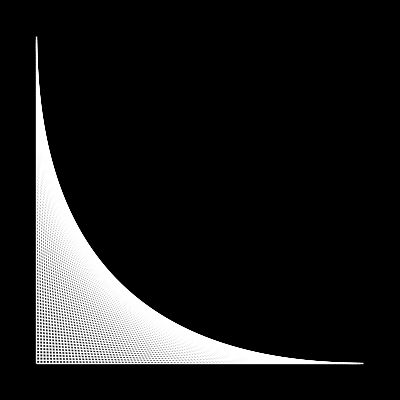

```mathematica
Show[Table[Graphics[{RGBColor[1,1,1],Line[{{0,1-n/100},{n/100,0}}]}],{n,0,100}],PlotRange->{{0,1},{0,1}},AspectRatio->1,Background->Black]
```

### 我的简化版

```mathematica
Graphics[{White,Line[Table[{{0,1-n/100},{n/100,0}},{n,0,100}]]},Background->Black,PlotRange->{{0,1},{0,1}}]
```

-Graphics-

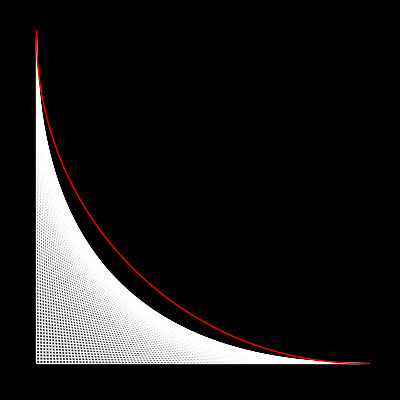

```mathematica
Graphics[{White,Line[Table[{{0,1-n/100},{n/100,0}},{n,0,100}]],Red,Circle[{1,1},1]},Background->Black,PlotRange->{{0,1},{0,1}}]
```

### 那么如何得到包络线的方程呢？